## Bounds on EDGB Theory From the Overall Posterior of GW150914

```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post_150914.csv","CSV"]; (*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/beta_150914.csv","CSV"];  (*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/alpha_150914.csv","CSV"] ;(*PPE alpha*)
```

```mathematica
χ1All=dataOverall1[[All,7]]; (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]];
```

```mathematica
m1All=dataOverall1[[All,5]]*tsolar/.tsolar->4.925491*10^-6;
m2All=dataOverall1[[All,6]]*tsolar/.tsolar->4.925491*10^-6;
```

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=1/1.64485*dataOverall2[[All,1]];(*1-sigma upper bound*)
αppEAll=1/1.64485*dataOverall3[[All,1]](*1-sigma upper bound*);
```

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2);
```

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] ;(*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*);
```

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll]; (*Sigma_Zeta from amplitude corrections*)
```

```mathematica
Length[m1All]
```

16332

```mathematica
Length[βppEAll]
```

16332

```mathematica
Mean[ζampAll]
```

13615.1

```mathematica
Mean[ζphaseAll]
```

2581.12

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

13241

```mathematica
Length[ζAllampSelected]
```

9685

```mathematica
Mean[ζAllphaseSelected]
```

0.166973

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.205828

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184,0.314749},{1},16328,{1},{-0.960167,432.955,7,0.304489,0.0668414}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184,0.314749,1.63394},16330,{-0.960167,432.955,8,0.0668414,0.335123}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] (*Data satisfying zeta_phase<1*)
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184},13239,{-0.960167,432.955,1.12358,4,0.423524,0.156429,0.304489}}
 |  |  |  |

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{-0.835255,614.169,2.3996,-1.15619,39.5694,34.4793,0.70691,0.434739,-0.100755,0.415459,0.0695161,0.364694},9683,{-0.960167,432.955,8,0.0668414,0.335123}}
 |  |  |  |

```mathematica
A4[[All,12]];
```

```mathematica
Length[A3]
```

13241

```mathematica
Length[A4]
```

9685

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.332056

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{44.4342,31.934,22.7704,227.58,57.7914,17.6663,62.6893,26.9488,16316,38.2305,22.6651,26.4395,26.7934,27.4281,17.6344,20.373,31.4995}
 |  |  |  |

{29.4374,21.1005,15.388,150.157,38.3316,12.3394,41.2486,18.1672,16316,25.8054,15.2911,17.7692,18.0106,18.4007,12.0978,14.0065,21.0506}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

50.495

```mathematica
Mean[SqrtαEDGBphase]
```

33.5149

```mathematica
tsolar=4.925491*10^-6
```

4.92549×10^-6

```mathematica
SqrtαEDGBphaseSelected=((A4[[All,11]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 ;(*square root of alpha_EDGB from phase correction of the data satisfying zeta_phase<1*)
```

```mathematica
SqrtαEDGBampSelected=((A4[[All,12]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 ;(*square root of alpha from amplitude correction of the data satisfying zeta_amp<1*)
```

```mathematica
Mean[SqrtαEDGBphaseSelected]
```

19.2054

```mathematica
Mean[SqrtαEDGBampSelected]
```

28.7194

(α^2)_EDGB from phase correction:

```mathematica
LogSquaredαPhase=Log[SqrtαEDGBphase^4] (*This is Log of sigma_(alpha^2)*)
```

{13.5291,12.1972,10.9343,20.0467,14.5851,10.0512,14.8785,11.5985,16316,13.0023,10.9091,11.5099,11.5638,11.6496,9.9721,10.5581,12.1877}
 |  |  |  |

```mathematica
MaxLogSquaredαPhase=Max[LogSquaredαPhase]
```

31.9617

```mathematica
MinLogSquaredαPhase=Min[LogSquaredαPhase]
```

8.84137

```mathematica
𝒟logα=HistogramDistribution[LogSquaredαPhase] ;
```

```mathematica
pslogαPhase=PDF[𝒟logα,x];
```

```mathematica
Histogram[LogSquaredαPhase];
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])] (*P(α^2|Subscript[σ, α^2])*)
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
αSampleLog=Prepend[10^Range[-7,15,0.1],0];(*Sample Subscript[σ, α^2] for integration. I decided to include 0 in the sample*)
```

```mathematica
fun1αphaseTable[y_]=Table[{αSampleLog[[i]],fun1αphase[αSampleLog[[i]],y]},{i,1,Length[αSampleLog]}]; (*Table for fun1αphase*)
```

```mathematica
αPhaseMC[x_]=pslogαPhase;
```

```mathematica
αPhaseMC[4]
```

0.

```mathematica
αPhaseMC[32]
```

0.

```mathematica
αMCSample=Range[3.5,35,1.2];
```

```mathematica
αMCTable=Table[{αMCSample[[i]],αPhaseMC[αMCSample[[i]]]},{i,1,Length[αMCSample]}];
```

```mathematica
αMCTableInterp=Interpolation[αMCTable];
```

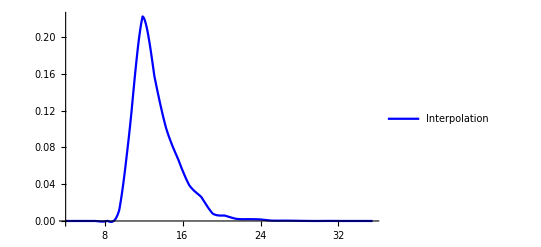

```mathematica
plotαMCTableInterp=Plot[αMCTableInterp[x],{x,4,35.5},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

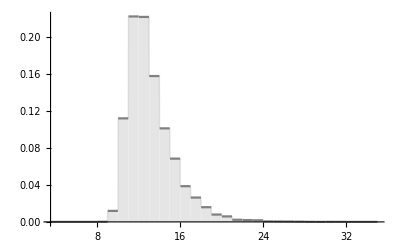

```mathematica
plot5=Plot[αPhaseMC[x],{x,3.5,35},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

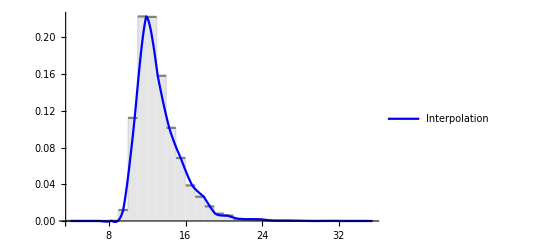

```mathematica
Show[plot5,plotαMCTableInterp] (*Interpolation matches the actual pdf of monte-carlo*)
```

```mathematica
αFinalPDFPhaseLog=Table[{fun1αphaseTable[y][[i,1]],NIntegrate[fun1αphaseTable[y][[i,2]]αMCTableInterp[y],{y,MinLogSquaredαPhase,MaxLogSquaredαPhase}]},{i,1,Length[fun1αphaseTable[y]]}];
```

```mathematica
αFinalPDFPhaseInterpLog=Interpolation[αFinalPDFPhaseLog];
```

```mathematica
αNormalization=NIntegrate[αFinalPDFPhaseInterpLog[x],{x,0,10^15}]
```

0.456707

```mathematica
αFinalPDFPhaseLogNorm=Table[{αFinalPDFPhaseLog[[i,1]],αFinalPDFPhaseLog[[i,2]]/αNormalization},{i,1,Length[αFinalPDFPhaseLog]}];
```

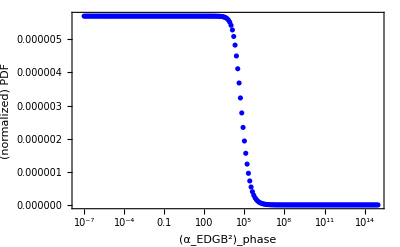

```mathematica
plotαFinalPDFPhaseLogNorm=ListLogLinearPlot[{αFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_phase","(normalized) PDF"}]
```

```mathematica
αFinalPDFPhaseInterpLogNorm=Interpolation[αFinalPDFPhaseLogNorm];
```

```mathematica
αFinalCDFPhaseNorm=Table[{αSampleLog[[i]],NIntegrate[αFinalPDFPhaseInterpLogNorm[x],{x,0,αSampleLog[[i]]}]},{i,1,Length[αSampleLog]}];
```

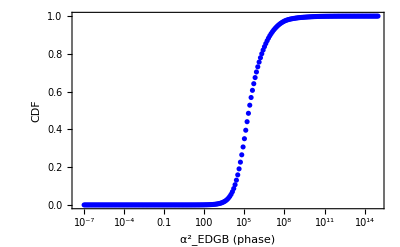

```mathematica
ListLogLinearPlot[αFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB (phase)","CDF"}]
```

```mathematica
αFinalCDFPhaseNormInterp=Interpolation[αFinalCDFPhaseNorm];
```

```mathematica
αSquared90CLphase=x/.FindRoot[αFinalCDFPhaseNormInterp[x]==0.9,{x,100}] (*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

8.60087×10^6

```mathematica
√√αSquared90CLphase//N
```

54.1546

```mathematica
Subscript[α^2, EDGB] from amplitude correction:
```

```mathematica
LogSquaredαamp=Log[SqrtαEDGBamp^4]
```

{15.176,13.8547,12.5018,21.71,16.2274,11.4866,16.5528,13.1758,16316,14.5745,12.4833,13.0994,13.1526,13.2463,11.4794,12.0568,13.7999}
 |  |  |  |

```mathematica
MaxLogSquaredαamp=Max[LogSquaredαamp]
```

33.6304

```mathematica
MinLogSquaredαamp=Min[LogSquaredαamp]
```

10.3987

```mathematica
𝒟logαamp=HistogramDistribution[LogSquaredαamp] ;
```

```mathematica
pslogαamp=PDF[𝒟logαamp,x];
```

```mathematica
Histogram[LogSquaredαamp];
```

```mathematica
αampMC[x_]=pslogαamp;
```

```mathematica
αampMC[34]
```

0.

```mathematica
αampMC[10.2]
```

0.00232672

```mathematica
αMCSampleamp=Range[9,35,1.09];
```

```mathematica
αMCTableamp=Table[{αMCSampleamp[[i]],αampMC[αMCSampleamp[[i]]]},{i,1,Length[αMCSampleamp]}];
```

```mathematica
αMCTableInterpamp=Interpolation[αMCTableamp];
```

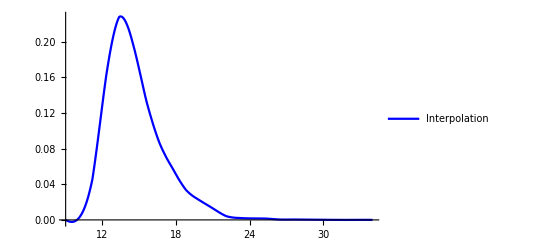

```mathematica
plotαMCTableInterpamp=Plot[αMCTableInterpamp[x],{x,9,34},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

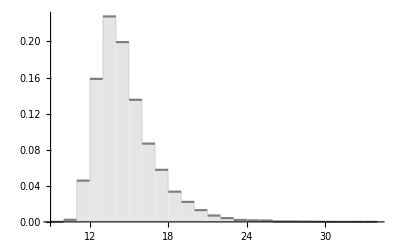

```mathematica
plot6=Plot[αampMC[x],{x,9,34},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

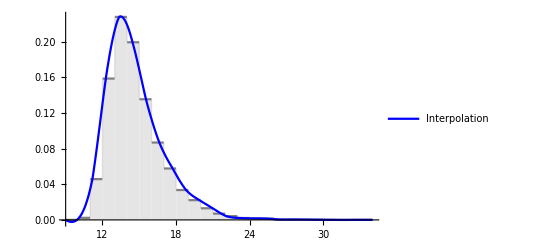

```mathematica
Show[plot6,plotαMCTableInterpamp]
```

```mathematica
αSampleLogamp=Prepend[10^Range[-7,15,0.1],0];
```

```mathematica
fun1αamp[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])];
```

```mathematica
fun1αampTable[y_]=Table[{αSampleLogamp[[i]],fun1αphase[αSampleLogamp[[i]],y]},{i,1,Length[αSampleLogamp]}];
```

```mathematica
αFinalPDFampLog=Table[{fun1αampTable[y][[i,1]],NIntegrate[fun1αampTable[y][[i,2]]αMCTableInterpamp[y],{y,MinLogSquaredαamp,MaxLogSquaredαPhase}]},{i,1,Length[fun1αampTable[y]]}];
```

```mathematica
αFinalPDFampInterpLog=Interpolation[αFinalPDFampLog]
```

InterpolatingFunction[…]

```mathematica
αNormalizationamp=NIntegrate[αFinalPDFampInterpLog[x],{x,0,10^15}]
```

0.540089

```mathematica
αFinalPDFampLogNorm=Table[{αFinalPDFampLog[[i,1]],αFinalPDFampLog[[i,2]]/αNormalizationamp},{i,1,Length[αFinalPDFampLog]}];
```

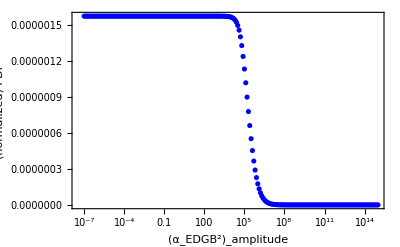

```mathematica
plotαFinalPDFampLogNorm=ListLogLinearPlot[{αFinalPDFampLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"(α_EDGB^2)_amplitude","(normalized) PDF"}]
```

```mathematica
αFinalPDFampInterpLogNorm=Interpolation[αFinalPDFampLogNorm];
```

```mathematica
αFinalCDFampNorm=Table[{αSampleLogamp[[i]],NIntegrate[αFinalPDFampInterpLogNorm[x],{x,0,αSampleLogamp[[i]]}]},{i,1,Length[αSampleLogamp]}];
```

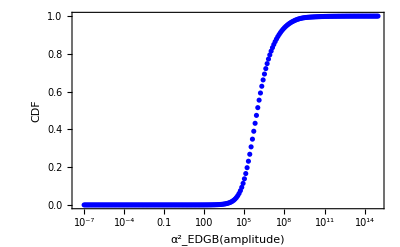

```mathematica
ListLogLinearPlot[αFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"α^2_EDGB(amplitude)","CDF"}]
```

```mathematica
αFinalCDFampNormInterp=Interpolation[αFinalCDFampNorm];
```

```mathematica
αSquared90CLamp=x/.FindRoot[αFinalCDFampNormInterp[x]==0.9,{x,1000}](*90% CL of Subscript[α^2, EDGB] from phase correction *)
```

3.75131×10^7

```mathematica
√√αSquared90CLamp
```

78.2611

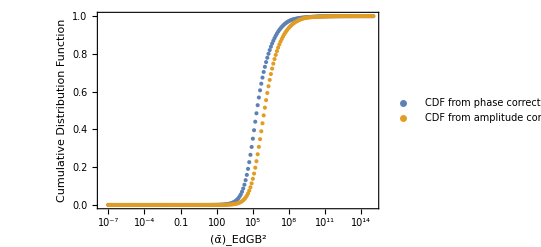

```mathematica
PlotCDFComparison=ListLogLinearPlot[{αFinalCDFPhaseNorm,αFinalCDFampNorm},PlotRange->All,TicksStyle->Directive["Label",14],AxesLabel->{nPN,Subscript[σ, α]},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction"},LabelStyle->{FontSize->5},LegendMarkerSize->10,LegendMargins->0,LegendFunction->"Frame"],{Left,Top}]},FrameLabel->{"(ᾱ)_EdGB^2","Cumulative Distribution Function"},Frame->True] (*Shows that indeed for GW150914, the amplitude and phase corrections are comparable*)
```

## ζ from phase correction

### 2D Gaussian, ζ samples

```mathematica
𝒟log=HistogramDistribution[Log[ζphaseAll]] (*simga_zeta from log of phase correction from monte-carlo. If we use the distribution of ζ, the pdf we get looks almost rectangular. That is why we are using the log[sigma_zeta]. We can compare their shapes from following two histograms *)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζphaseAll]];
```

```mathematica
Histogram[ζphaseAll];
```

```mathematica
ps1=PDF[𝒟log,x];
```

```mathematica
ps2[x]=ps1;
```

```mathematica
plottest2=Plot[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]},Filling->Axis,PlotStyle->Gray,PlotRange->All];
```

```mathematica
zeta1=ListLinePlot[{{0,0},{0,0.25}},PlotStyle->Red];
```

```mathematica
Show[plottest2,zeta1,Frame->True,PlotRange->All] ;(*Shows how much of the area under the curve satisfies zeta<1 from phase correction*)
```

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]
```

0.999333

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]*100 (*81% area under the curve satisfies zeta<1 from phase correction*)
```

81.0666

```mathematica
MaxLogζphase=Log[Max[ζphaseAll]]
```

17.1488

```mathematica
MinLogζphase=Log[Min[ζphaseAll]]
```

-5.86967

```mathematica
fun1kent[x_,y_]=1/(√(2*π) Exp[y])*Exp[-x^2/(2Exp[2y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

ζ sample

```mathematica
ζSampleLog=Prepend[10^Range[-5,6,0.1],0];
```

Creating a table for fun1Kent[x,y] at each ζ sample for x

```mathematica
fun1TableLog[y_]=Table[{ζSampleLog[[i]],fun1kent[ζSampleLog[[i]],y]},{i,1,Length[ζSampleLog]}];
```

```mathematica
ζMC[x_]=ps1;
```

```mathematica
ζMC[-6.5]
```

0.

```mathematica
ζMC[18]
```

0.

ζ sample for creating an interpolation function for the MC prob distribution
Since ζ > 0, I only consider positive ζ

```mathematica
ζMCSample=Range[-9.5,18,1];
```

creating a table for the MC distribution at each sample ζ

```mathematica
ζMCTable=Table[{ζMCSample[[i]],ζMC[ζMCSample[[i]]]},{i,1,Length[ζMCSample]}];
```

creating an interpolation function

```mathematica
ζMCTableInterp=Interpolation[ζMCTable];
```

Plot

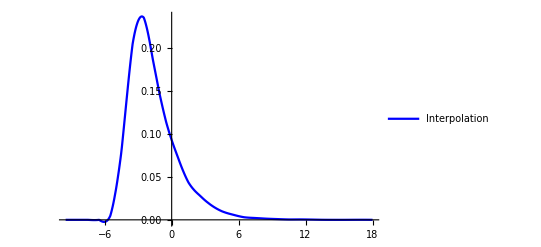

```mathematica
plotζMCTableInterp=Plot[ζMCTableInterp[x],{x,-9.5,18},PlotStyle->Blue,PlotLegends->{"Interpolation"}]
```

Comparison with the actual distribution

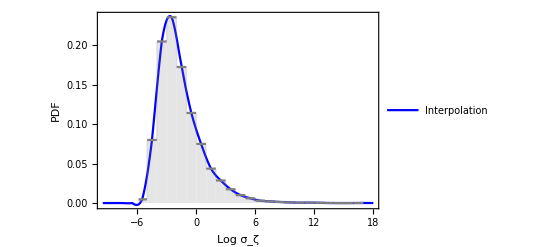

```mathematica
Show[plotζMCTableInterp,plottest2,Frame->True,FrameLabel->{"Log σ_ζ","PDF"}]
```

```mathematica
ζFinalPDFPhaseLog=Table[{fun1TableLog[y][[i,1]],NIntegrate[fun1TableLog[y][[i,2]]ζMCTableInterp[y],{y,MinLogζphase,MaxLogζphase}]},{i,1,Length[fun1TableLog[y]]}];
```

#### Normalized Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLog=Interpolation[ζFinalPDFPhaseLog];
```

Normalization

```mathematica
Normalization=NIntegrate[ζFinalPDFPhaseInterpLog[x],{x,0,10^6}]
```

0.50005

Normalized distribution

```mathematica
ζFinalPDFPhaseLogNorm=Table[{ζFinalPDFPhaseLog[[i,1]],ζFinalPDFPhaseLog[[i,2]]/Normalization},{i,1,Length[ζFinalPDFPhaseLog]}];
```

Plot

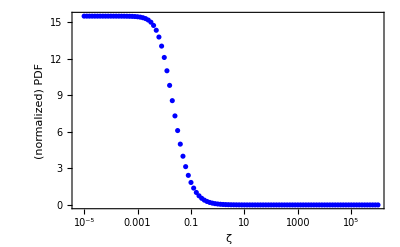

```mathematica
plotζFinalPDFPhaseLogNorm=ListLogLinearPlot[{ζFinalPDFPhaseLogNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}]
```

#### Cumulative Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLogNorm=Interpolation[ζFinalPDFPhaseLogNorm];
```

Creating a table for cumulative distribution

```mathematica
ζFinalCDFPhaseNorm=Table[{ζSampleLog[[i]],NIntegrate[ζFinalPDFPhaseInterpLogNorm[x],{x,0,ζSampleLog[[i]]}]},{i,1,Length[ζSampleLog]}];
```

Plot

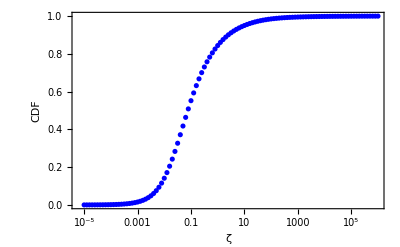

```mathematica
ListLogLinearPlot[ζFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}]
```

CDF nicely asymptotes to 1 (suggesting that ζ = 100 is large enough)

#### Finding 90% credible limit for ζ

Interpolation for CDF

```mathematica
ζFinalCDFPhaseNormInterp=Interpolation[ζFinalCDFPhaseNorm]
```

InterpolatingFunction[…]

90% limit

```mathematica
ζ90CLphase=x/.FindRoot[ζFinalCDFPhaseNormInterp[x]==0.9,{x,0.02}]
```

2.45602

```mathematica
ζ  from amplitude correction
```

amplitude correction from ζ

```mathematica
𝒟logamp=HistogramDistribution[Log[ζampAll]] (*zeta from log of amp correction from monte-carlo*)
```

DataDistribution[…]

```mathematica
Histogram[Log[ζampAll]];
```

```mathematica
Histogram[ζampAll];
```

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
MinLogζamp=Min[Log[ζampAll]]
```

-4.56772

```mathematica
MaxLogζamp=Max[Log[ζampAll]]
```

18.8174

```mathematica
plottestamp=Plot[ps2amp[x],{x,-5,20},Filling->Axis,PlotStyle->Gray];
```

```mathematica
Show[plottestamp,zeta1,Frame->True,PlotRange->All] ;(*Shows how much of the area under the curve satisfies zeta<1 from amplitude correction*)
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]
```

0.999671

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]*100 (*59.3% area under the curve satisfies zeta<1 from amplitude correction*)
```

59.2885

```mathematica
ζSampleLogamp=Prepend[10^Range[-5,9,0.1],0];
```

```mathematica
fun1TableLogamp[y_]=Table[{ζSampleLogamp[[i]],fun1kent[ζSampleLogamp[[i]],y]},{i,1,Length[ζSampleLogamp]}];
```

```mathematica
ζMCamp[x_]=ps1amp;
```

```mathematica
ζMCamp[-5.5]
ζMCamp[19]
```

0.

0.

```mathematica
ζMCSampleamp=Range[-20,25,1.02];
```

```mathematica
ζMCTableamp=Table[{ζMCSampleamp[[i]],ζMCamp[ζMCSampleamp[[i]]]},{i,1,Length[ζMCSampleamp]}];
```

```mathematica
ζMCTableInterpamp=Interpolation[ζMCTableamp];
```

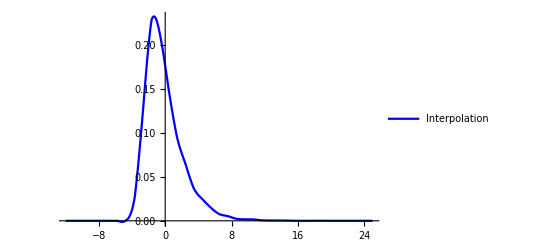

```mathematica
plotζMCTableInterpamp=Plot[ζMCTableInterpamp[x],{x,-12,25},PlotStyle->Blue,PlotLegends->{"Interpolation"},PlotRange->All]
```

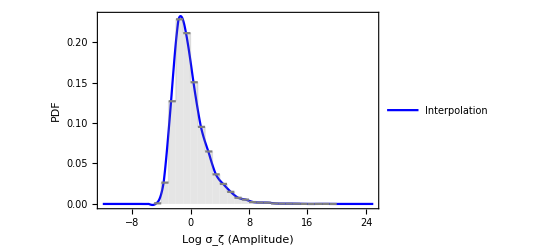

```mathematica
Show[plotζMCTableInterpamp,plottestamp,Frame->True,FrameLabel->{"Log σ_ζ (Amplitude)","PDF"}]
```

```mathematica
ζFinalPDFampLog=Table[{fun1TableLogamp[y][[i,1]],NIntegrate[fun1TableLogamp[y][[i,2]]ζMCTableInterpamp[y],{y,MinLogζamp,MaxLogζamp}]},{i,1,Length[fun1TableLogamp[y]]}];
```

```mathematica
ζFinalPDFampInterpLog=Interpolation[ζFinalPDFampLog];
```

Normalization

```mathematica
Normalizationζamp=NIntegrate[ζFinalPDFampInterpLog[x],{x,0,10^9}]
```

0.509751

```mathematica
ζFinalPDFampLogNorm=Table[{ζFinalPDFampLog[[i,1]],ζFinalPDFampLog[[i,2]]/Normalizationζamp},{i,1,Length[ζFinalPDFampLog]}];
```

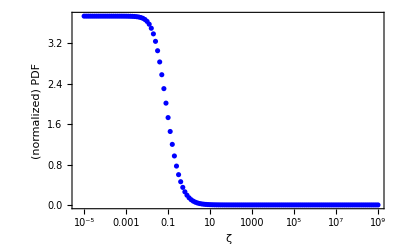

```mathematica
plotζFinalPDFampLogNorm=ListLogLinearPlot[{ζFinalPDFampLogNorm},PlotRange->Full,Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"ζ","(normalized) PDF"}]
```

```mathematica
ζFinalPDFampInterpLogNorm=Interpolation[ζFinalPDFampLogNorm];
```

```mathematica
ζFinalCDFampNorm=Table[{ζSampleLogamp[[i]],NIntegrate[ζFinalPDFampInterpLogNorm[x],{x,0,ζSampleLogamp[[i]]}]},{i,1,Length[ζSampleLogamp]}];
```

```mathematica
ListLogLinearPlot[ζFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}];
```

```mathematica
ζFinalCDFampNormInterp=Interpolation[ζFinalCDFampNorm];
```

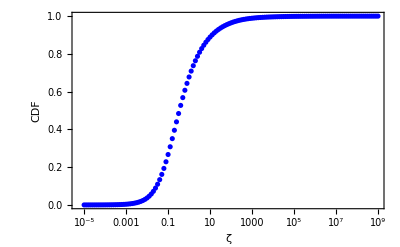

```mathematica
ListLogLinearPlot[ζFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue},FrameLabel->{"ζ","CDF"}]
```

```mathematica
ζ90CLamp=x/.FindRoot[ζFinalCDFampNormInterp[x]==0.9,{x,12}]
```

12.3832